```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
ρ=1-1/10^13;
SIGMA={{1,ρ},{ρ,1}};
U[x_,y_]=N[1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]]];
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
(*outbnd[{x_,y_}]:=x<0;*)
```

```mathematica
SIGMA//MatrixForm
```

(1 | 9999999999999/10000000000000
9999999999999/10000000000000 | 1)

```mathematica
(*hmc[U_,dU_,ddU_,Dim_,BURNIN_,EPISODE_,vanilla0_,switch_,qinit_]:=Module[{qAll,pAll,hess,UE,ES,Utotal,Ktotal,hi,lo,decayenergy=DECAYENERGY,decaydt=DECAYDT,dt1=dt10,decayfactor=10^(-1/BURNIN),dt2=dt20,Htotal,ii=1,s,S,AS,KtotalNew,dt,p,q0,α,q,j,bad,Htotal1,Htotal2,i,q1,ND=NormalDistribution[0,1],UD=UniformDistribution[],QS=ConstantArray[0, {(EPISODE-BURNIN)CHAINS,Dim}],vanilla=vanilla0,ACS={}},
If[qinit!={},qAll=qinit,qAll=RandomVariate[ND,{CHAINS,Dim}]];Utotal=Sum[Apply[ U,qAll[[i]]],{i,1,CHAINS}];Htotal1=2Utotal;Htotal2=2Utotal;For[j=1,j⩽EPISODE,j++,
Htotal=If[vanilla,Htotal1,Htotal2];dt=If[vanilla,dt1,dt2];
US={};
AS={};
ES={};
For[i=1,i<=CHAINS,i++,
bad=False;
q=qAll[[i]];
p=RandomVariate[ND,Dim];KtotalNew = If[vanilla,p.p,p.If[diag,p/Apply[ddU,q],LinearSolve[Apply[ddU,q],p,Method->"Krylov"]]]/2;Utotal=Apply[ U,q];
Ktotal=Htotal-Utotal;
p=p Sqrt[Abs[Ktotal/KtotalNew]];
q0=q;If[j<=BURNIN,UE={Apply[U,q]}];Do[p=p-dt Apply[dU,q];q1=q;q=q+dt If[vanilla,p,If[diag,p/Apply[ddU,q],LinearSolve[Apply[ddU,q],p,Method->"Krylov"]]];If[outbnd[q],
bad=True;q=q1];
If[j<=BURNIN,UE=Append[UE,Apply[U,q]]],STEPS];If[j<=BURNIN,ES=Append[ES,UE]];α=If[bad,0,Exp[Clip[Apply[U,q0]-Apply[U,q],{-20,0}]]];AS=Append[AS,N[α]];If[α<RandomVariate[UD],q=q0];qAll[[i]]=q;If[j>BURNIN,QS[[ii,;;]]=q;ii=ii+1];
(*If[j>BURNIN && i==1,QS[[ii]]=(*Apply[U,q]+*)If[vanilla,p.p,p.If[diag,p/Apply[ddU,q],LinearSolve[Apply[ddU,q],p,Method->"Krylov"]]]/2;ii=ii+1];
*)US=Append[US,Apply[U,q]];
];If[Mod[j,INTERVAL]==0,Print[Row[{j,Ktotal,KtotalNew,Mean[AS],StandardDeviation[AS],Utotal,Htotal1,Htotal2,dt1,dt2,vanilla,s,S},"     "]]];If[j<=BURNIN,
s=Union[Flatten[Table[Ordering[ES[[i]],1],{i,1,CHAINS}]]];S=Union[Flatten[Table[Ordering[ES[[i]],-1],{i,1,CHAINS}]]];If[s=={1,STEPS+1}&&S=={1,STEPS+1},dt=dt (1+decaydt)];If[s=={1}&&S=={STEPS+1},dt=dt/(1+decaydt)];hi=Mean[AS]>HIGHAP;lo=Mean[AS]<LOWAP;
Utotal=Mean[US];If[hi,Htotal=(Htotal-Utotal)(1+decayenergy)+Utotal,If[lo,Htotal=(Htotal-Utotal)/(1+decayenergy)+Utotal]]];If[vanilla,
Htotal1=Htotal;dt1=dt,
Htotal2=Htotal;dt2=dt];
If[switch && j>switch0,vanilla=Not[vanilla]]];QS];*)
```

```mathematica
(*hmc1[U_,dU_,ddU_,Dim_,BURNIN_,EPISODE_,vanilla0_,switch_,qinit_]:=Module[{qAll,pAll,hess,UE,ES,Utotal,Ktotal,hi,lo,decayenergy=DECAYENERGY,decaydt=DECAYDT,dt1=dt10,dt2=dt20,Htotal,s,S,AS,KtotalNew,dt,p,q0,α,q,j,bad,Htotal1,Htotal2,i,q1,ND=NormalDistribution[0,1],
UD=UniformDistribution[],QS=List[],vanilla=vanilla0,ACS={}},
If[qinit!={},qAll=qinit,qAll=RandomVariate[ND,Dim]];
Utotal=Apply[ U,qAll];
Htotal1=2Utotal;
Htotal2=2Utotal;
AS={};ES={};
For[j=1,j⩽EPISODE,j++,
pAll=RandomVariate[ND,Dim];KtotalNew = If[vanilla,pAll.pAll,pAll.If[diag,pAll/Apply[ddU,qAll],LinearSolve[Apply[ddU,qAll],pAll,Method->"Krylov"]]]/2;Utotal=Apply[ U,qAll];Htotal=If[vanilla,Htotal1,Htotal2];dt=If[vanilla,dt1,dt2];Ktotal=Htotal-Utotal;pAll=pAll Sqrt[Abs[Ktotal/KtotalNew]];bad=False;p=pAll;q=qAll;q0=q;If[j<=BURNIN,UE={Apply[U,q]}];Do[p=p-dt Apply[dU,q];q1=q;q=q+dt If[vanilla,p,If[diag,p/Apply[ddU,q],LinearSolve[Apply[ddU,q],p,Method->"Krylov"]]];If[outbnd[q],
bad=True;q=q1];
If[j<=BURNIN,UE=Append[UE,Apply[U,q]]],STEPS];
α=If[bad,0,Exp[Clip[Apply[U,q0]-Apply[U,q],{-20,0}]]];
If[α<RandomVariate[UD],q=q0];
qAll=q;
If[j>BURNIN,QS=Append[QS,q]];
If[j<=BURNIN,
ES=Append[ES,UE];AS=Append[AS,N[α]];
If[Length[ES]>CHAINS,ES=Delete[ES,1]];If[Length[AS]>CHAINS,AS=Delete[AS,1]]];If[Mod[j,INTERVAL]==0,Print[Row[{j,Ktotal,KtotalNew,Mean[AS],StandardDeviation[AS],Utotal,Htotal1,Htotal2,dt1,dt2,vanilla,s,S},"     "]]];If[j<=BURNIN&&j>CHAINS,
s=Union[Flatten[Table[Ordering[ES[[i]],1],{i,1,CHAINS}]]];S=Union[Flatten[Table[Ordering[ES[[i]],-1],{i,1,CHAINS}]]];If[s=={1,STEPS+1}&&S=={1,STEPS+1},dt=dt (1+decaydt)];If[s=={1}&&S=={STEPS+1},dt=dt/(1+decaydt)];hi=Mean[AS]>HIGHAP;lo=Mean[AS]<LOWAP;If[hi,Htotal=(Htotal-Utotal)(1+decayenergy)+Utotal,If[lo,Htotal=(Htotal-Utotal)/(1+decayenergy)+Utotal]];If[vanilla,
Htotal1=Htotal;dt1=dt,
Htotal2=Htotal;dt2=dt]];If[switch && j>switch0,vanilla=Not[vanilla]]];QS];*)
```

```mathematica
(*hmc[U_,dU_,ddU_,Dim_,BURNIN_,EPISODE_,vanilla0_,switch_,qinit_]:=Module[{qAll,pAll,hess,UE,ES,Utotal,Ktotal,hi,lo,decayenergy=DECAYENERGY,decaydt=DECAYDT,dt1=dt10,dt2=dt20,Htotal,ii=1,s,S,AS,KtotalNew,dt,p,q0,α,q,j,bad,Htotal1,Htotal2,i,q1,ND=NormalDistribution[0,1],UD=UniformDistribution[],QS=ConstantArray[0,{CHAINS( EPISODE-BURNIN),Dim}],vanilla=vanilla0,ACS={}},
If[qinit!={},qAll=qinit,qAll=RandomVariate[ND,{CHAINS,Dim}]];Utotal=Sum[Apply[ U,qAll[[i]]],{i,1,CHAINS}];Htotal1=2Utotal;Htotal2=2Utotal;
For[j=1,j⩽EPISODE,j++,
pAll=RandomVariate[ND,{CHAINS,Dim}];KtotalNew = Sum[If[vanilla,pAll[[i]].pAll[[i]],pAll[[i]].If[diag,pAll[[i]]/Apply[ddU,qAll[[i]]],LinearSolve[Apply[ddU,qAll[[i]]],pAll[[i]],Method->"Krylov"]]]/2,{i,1,CHAINS}];Utotal=Sum[Apply[ U,qAll[[i]]],{i,1,CHAINS}];Htotal=If[vanilla,Htotal1,Htotal2];dt=If[vanilla,dt1,dt2];Ktotal=Htotal-Utotal;pAll=pAll Sqrt[Abs[Ktotal/KtotalNew]];AS={};ES={};For[i=1,i<=CHAINS,i++,
bad=False;
p=pAll[[i]];
q=qAll[[i]];
q0=q;
If[j<=BURNIN,UE={Apply[U,q]}];Do[p=p-dt Apply[dU,q];q1=q;q=q+dt If[vanilla,p,If[diag,p/Apply[ddU,q],LinearSolve[Apply[ddU,q],p,Method->"Krylov"]]];If[outbnd[q],
bad=True;q=q1];
If[j<=BURNIN,UE=Append[UE,Apply[U,q]]],STEPS];
If[j<=BURNIN,ES=Append[ES,UE]];α=If[bad,0,Exp[Clip[Apply[U,q0]-Apply[U,q],{-20,0}]]];AS=Append[AS,N[α]];If[α<RandomVariate[UD],q=q0];qAll[[i]]=q;If[j>BURNIN,QS[[ii,;;]]=q;ii=ii+1]];If[Mod[j,INTERVAL]==0,Print[Row[{j,Ktotal,KtotalNew,Mean[AS],StandardDeviation[AS],Utotal,Htotal1,Htotal2,dt1,dt2,vanilla,s,S},"     "]]];If[j<=BURNIN,
s=Union[Flatten[Table[Ordering[ES[[i]],1],{i,1,CHAINS}]]];S=Union[Flatten[Table[Ordering[ES[[i]],-1],{i,1,CHAINS}]]];If[s=={1,STEPS+1}&&S=={1,STEPS+1},dt=dt (1+decaydt)];If[s=={1}&&S=={STEPS+1},dt=dt/(1+decaydt)];hi=Mean[AS]>HIGHAP;lo=Mean[AS]<LOWAP;If[hi,Htotal=(Htotal-Utotal)(1+decayenergy)+Utotal,If[lo,Htotal=(Htotal-Utotal)/(1+decayenergy)+Utotal]]];If[vanilla,
Htotal1=Htotal;dt1=dt,
Htotal2=Htotal;dt2=dt];
If[switch && j>switch0,
vanilla=Not[vanilla]]];QS];*)
```

```mathematica
(*hmc[U_,dU_,ddU_,Dim_,BURNIN_,EPISODE_,vanilla0_,switch_,qinit_]:=Module[{qAll,pAll,hess,UE,ES,Utotal,Ktotal,hi,lo,decayenergy=DECAYENERGY,decaydt=DECAYDT,dt1=dt10,decayfactor=10^(-1/BURNIN),dt2=dt20,Htotal,ii=1,s,S,AS,KtotalNew,dt,p,q0,α,q,j,bad,Htotal1,p0,Htotal2,i,q1,ND=NormalDistribution[0,1],UD=UniformDistribution[],QS=ConstantArray[0, EPISODE-BURNIN],vanilla=vanilla0,ACS={}},
If[qinit!={},qAll=qinit,qAll=RandomVariate[ND,{CHAINS,Dim}]];Utotal=Sum[Apply[ U,qAll[[i]]],{i,1,CHAINS}];Htotal1=2Utotal;Htotal2=2Utotal;For[j=1,j⩽EPISODE,j++,
pAll=RandomVariate[ND,{CHAINS,Dim}];KtotalNew = Sum[If[vanilla,pAll[[i]].pAll[[i]],pAll[[i]].If[diag,pAll[[i]]/Apply[ddU,qAll[[i]]],LinearSolve[Apply[ddU,qAll[[i]]],pAll[[i]],Method->"Krylov"]]]/2,{i,1,CHAINS}];Utotal=Sum[Apply[ U,qAll[[i]]],{i,1,CHAINS}];Htotal=If[vanilla,Htotal1,Htotal2];dt=If[vanilla,dt1,dt2];Ktotal=Htotal-Utotal;pAll=pAll Sqrt[Abs[Ktotal/KtotalNew]];AS={};ES={};For[i=1,i<=CHAINS,i++,
bad=False;
p=pAll[[i]];
q=qAll[[i]];
q0=q;
p0=p;If[j<=BURNIN,UE={Apply[U,q]}];Do[p=p-dt Apply[dU,q];q1=q;q=q+dt If[vanilla,p,If[diag,p/Apply[ddU,q],LinearSolve[Apply[ddU,q],p,Method->"Krylov"]]];If[outbnd[q],
bad=True;q=q1];If[j<=BURNIN,UE=Append[UE,Apply[U,q]]],STEPS];If[j<=BURNIN,ES=Append[ES,UE]];α=If[bad,0,Exp[Clip[Apply[U,q0]-Apply[U,q],{-20,0}]]];AS=Append[AS,N[α]];If[α<RandomVariate[UD],q=q0;p=p0];qAll[[i]]=q;If[j>BURNIN && i==1,QS[[ii]]=(*Apply[U,q]+*)If[vanilla,p.p,p.If[diag,p/Apply[ddU,q],LinearSolve[Apply[ddU,q],p,Method->"Krylov"]]]/2;ii=ii+1]];If[Mod[j,INTERVAL]==0,Print[Row[{j,Ktotal,KtotalNew,Mean[AS],StandardDeviation[AS],Utotal,Htotal1,Htotal2,dt1,dt2,vanilla,s,S},"     "]]];If[j<=BURNIN,
s=Union[Flatten[Table[Ordering[ES[[i]],1],{i,1,CHAINS}]]];S=Union[Flatten[Table[Ordering[ES[[i]],-1],{i,1,CHAINS}]]];If[s=={1,STEPS+1}&&S=={1,STEPS+1},dt=dt (1+decaydt)];If[s=={1}&&S=={STEPS+1},dt=dt/(1+decaydt)];hi=Mean[AS]>HIGHAP;lo=Mean[AS]<LOWAP;If[hi,Htotal=(Htotal-Utotal)(1+decayenergy)+Utotal,If[lo,Htotal=(Htotal-Utotal)/(1+decayenergy)+Utotal]]];If[vanilla,
Htotal1=Htotal;dt1=dt,
Htotal2=Htotal;dt2=dt];
If[switch ,
vanilla=Not[vanilla]]];QS];*)
```

```mathematica
(*INTERVAL=1001;
STEPS=3;
CHAINS=3;
switch0=1;
dt10=0.000000000000001;
dt20=0.000000000000001;
*)
(*STEPS=10;
CHAINS=10;
dt10=0.000000000000001;
dt20=0.000000000000001;*)
(*DECAYENERGY=0.05;
DECAYDT=0.05;
*)
(*CHAINS=10;
STEPS=10;*)
Dim=2;
(*qinit=RandomVariate[UniformDistribution[],{CHAINS,Dim}];*)
QS=hmc[U,dU,ddU,2,20000,30000,True,True,{}];
```

10010.4083295.271740.3678080.5499314.035974.4443447989.5.99717×10^-70.00122846True{1,3}{1,4}

2002721471.3.01730.1974350.14363213.327114.1274721485.5.99717×10^-70.00092296False{1}{3}

3003-0.9373713.900184.30627×10^-76.98073×10^-721.870420.93312.05845×10^65.99717×10^-70.000520987True{1,2}{4}

40044.41243×10^65.52050.5705720.37475618.073818.17894.41245×10^65.99717×10^-70.000200863False{1}{3}

50050.4482052.746330.3074360.5323527.820318.268523.26532×10^75.99717×10^-70.000113382True{1,3}{1,4}

60065.25882×10^70.3477640.3457460.56681220.065118.98975.25882×10^75.99717×10^-70.000103074False{1}{3}

7007-0.909123.219370.0006381690.0011053310.6289.718843.95103×10^75.99717×10^-70.0000851855True{1}{4}

80083.26531×10^71.849210.6259520.31736916.731914.95033.26532×10^75.99717×10^-70.000166002False{1}{3}

90091.202111.529412.58818×10^-74.44716×10^-718.971820.17392.45328×10^75.99717×10^-70.000137192True{1,2}{4}

100107.10627×10^61.221350.6594710.57027925.085322.02087.10629×10^65.99717×10^-70.000182603False{1,4}{2,3}

11011-0.2157292.701090.002768010.0047943321.04720.83124.41246×10^65.99717×10^-70.000430568True{1,2}{4}

120122.73977×10^66.946450.2844630.28569223.077323.53772.7398×10^65.99717×10^-70.000473624False{1}{3}

130131.19772.466510.3333330.5773521.516422.71413.01377×10^65.99717×10^-70.000430568True{1,4}{1,4}

140141.14447×10^71.561070.1856570.17016714.562213.71691.14447×10^75.99717×10^-70.000243044False{1,4}{2,3}

1501550.98952.938480.5204680.4700434.9779155.96741.84318×10^75.45197×10^-70.000137192True{1,4}{1,4}

160161.14447×10^70.7813810.3885880.5338263.30786940.1491.14447×10^75.45197×10^-70.000243044False{1}{2}

170171134.713.004050.4607210.3093112.290291137.2.0275×10^75.45197×10^-70.000182603True{1,3}{1,4}

180187.81688×10^60.8600080.4796070.47675.103761375.177.81688×10^65.45197×10^-70.000243044False{1,2}{2,3}

190191031.713.598680.3381070.5732171.180561032.895.33904×10^65.45197×10^-70.000267349True{1,2,4}{1,4}

200205.87293×10^62.24180.3852640.5343073.699581033.165.87294×10^65.45197×10^-70.000323492False{1,4}{1,4}

210211026.461.211730.223410.2101726.695431033.165.87294×10^65.45197×10^-70.000323492True{1,4}{1,4}

220225.87294×10^61.483130.3272330.3009071.873971033.165.87294×10^65.45197×10^-70.000323492False{1,4}{1,4}

230231031.782.601640.75190.3550521.37161033.165.87294×10^65.45197×10^-70.000323492True{1,4}{1,4}

240245.87294×10^60.01747660.3460250.5664462.419831033.165.87294×10^65.45197×10^-70.000323492False{1,4}{1,4}

250251031.294.860330.6041370.2862871.861241033.165.87294×10^65.45197×10^-70.000323492True{1,4}{1,4}

260265.87293×10^69.247480.6258690.3254673.938481033.165.87294×10^65.45197×10^-70.000323492False{1,4}{1,4}

270271026.882.832020.6377020.4989896.271971033.165.87294×10^65.45197×10^-70.000323492True{1,4}{1,4}

280285.87294×10^63.252330.3808770.2776511.861791033.165.87294×10^65.45197×10^-70.000323492False{1,4}{1,4}

290291030.020.6115190.3369820.5742153.130711033.165.87294×10^65.45197×10^-70.000323492True{1,4}{1,4}

```mathematica
(*QQ=Table[QS[[i;;Length[QS];;2]],{i,1,2}];*)
```

```mathematica
(*QQ//Dimensions*)
```

```mathematica
(*GraphicsRow[{Histogram[QQ[[1,;;]],Automatic,"Probability",PlotLabel->Subscript[K, HMC]],Histogram[QQ[[2,;;]],Automatic,"Probability",PlotLabel->Subscript[K, RMHMC]]}]
*)
```

{1.00683,0.996936}

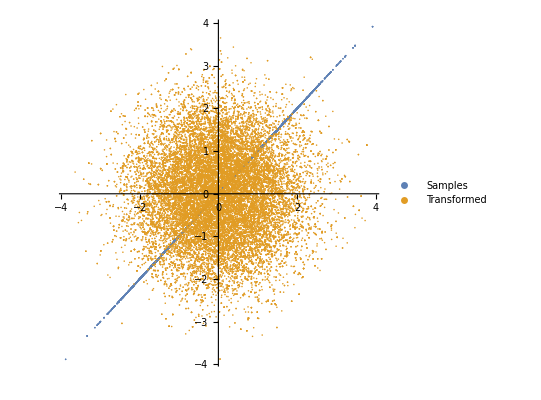

```mathematica
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[{QS,QS1},PlotStyle->Opacity[1],AspectRatio->1,PlotLegends->{Samples, Transformed}]
```

```mathematica
(*(*QS=hmc0[U,dU,ddU,2,5000,10000,True];*)
ListPlot[QS,PlotLabel->CHMC,PlotStyle->Opacity[.2],AspectRatio->1]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1,PlotStyle->Opacity[.1]]*)
```

```mathematica
(*QS=hmc[U,dU,ddU,2,5000,10000,True,False,{}];
ListPlot[QS,PlotLabel->HMC,PlotStyle->Opacity[.1]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1,PlotStyle->Opacity[.1]]*)
```

```mathematica
(*QS=hmc[U,dU,ddU,2,5000,10000,False,False,{}];
ListPlot[QS,PlotLabel->RHMC,PlotStyle->Opacity[.2]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1,PlotStyle->Opacity[.1]]*)
```